```mathematica
Inv[Jone_,Jtwo_] := Piecewise[{{ArcCos[-Jone/(4*Jtwo)],Jone<4*Jtwo},{Pi,Jone>4*Jtwo}}]
```

```mathematica
G11[J_,Jone_,Jtwo_,p_,zR_Real]:=NIntegrate[(p ((-J+Jtwo-zR)-Jone Cos[k]-(2 Jtwo) Cos[k]^2))/((2 π) ((J^2-2 J Jtwo-zR^2)+(2 J Jone) Cos[k]+(4 J Jtwo) Cos[k]^2)),{k,-π,π}]
```

```mathematica
G22[J_,Jone_,Jtwo_,p_,zR_Real]:=NIntegrate[(p ((-J+Jtwo+zR)-Jone Cos[k]-(2 Jtwo) Cos[k]^2))/((2 π) ((J^2-2 J Jtwo-zR^2)+(2 J Jone) Cos[k]+(4 J Jtwo) Cos[k]^2)),{k,-π,π}]
```

```mathematica
G12[J_,Jone_,Jtwo_,p_,zR_Real]:=NIntegrate[(p (Jtwo+Jone Cos[k]+(2 Jtwo) Cos[k]^2))/((2 π) ((J^2-2 J Jtwo-zR^2)+(2 J Jone) Cos[k]+(4 J Jtwo) Cos[k]^2)),{k,-π,π}]
```

```mathematica
Nulls[Jtwo_,z_]:=1-G11[1,0.2,Jtwo,-0.1,z]-G22[1,0.2,Jtwo,-0.1,z]-G12[1,0.2,Jtwo,-0.1,z]^2+G11[1,0.2,Jtwo,-0.1,z]G22[1,0.2,Jtwo,-0.1,z]
FindRoot[Nulls[0.,z]==0,{z,0.7536715765093541}]
```

{z→0.753672}

```mathematica
Lister[Plusminus_,Xstart_,StartIteration_] := Module[{lst={{Xstart,FindRoot[Nulls[Xstart,z],{z,StartIteration}]}}},
Do[
Jtwoo=Plusminus(n+1)*0.005;
p=FindRoot[Nulls[Jtwoo,z]==0,{z,z/.lst[[n,2]]}
];
AppendTo[lst,{Jtwoo,p}];
,{n,1,19,1}
];
lst
]
```

```mathematica
moduler[list_] := Module[{lst := {}},
Do [
AppendTo [lst,{list[[n,1]],z/.list[[n,2]]}];
,{n,1,20,1}
];
lst
]
```

```mathematica
ListPlot[moduler[Lister[-1,-0.005,0.8545]],moduler[Lister[1,0.005,0.8545]]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {2.31933}. NIntegrate obtained 2.39699 and 2.39164 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {2.31933}. NIntegrate obtained 0.147788 and 0.201551 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {2.31933}. NIntegrate obtained 0.0644472 and 0.014722 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

ListPlot::nonopt: Options expected (instead of {{0.005,0.854493},{0.01,0.854496},{0.015,0.854516},{0.02,0.854509},{0.025,0.854513},{0.03,0.854578},{0.035,0.854607},{0.04,0.854632},{0.045,0.854649},{0.05,0.854658},«10»}) beyond position 1 in ListPlot[{{-0.005,0.854489},{-0.01,0.854521},{-0.015,0.854518},{-0.02,0.854627},{-0.025,0.854706},{-0.03,0.854697},{-0.035,0.854723},{-0.04,0.854822},{-0.045,0.854853},{-0.05,0.854963},«10»},{{0.005,0.854493},{0.01,0.854496},{0.015,0.854516},{0.02,0.854509},{0.025,0.854513},{0.03,0.854578},{0.035,0.854607},{0.04,0.854632},{0.045,0.854649},{0.05,0.854658},«10»}]. An option must be a rule or a list of rules.

ListPlot[{{-0.005,0.854489},{-0.01,0.854521},{-0.015,0.854518},{-0.02,0.854627},{-0.025,0.854706},{-0.03,0.854697},{-0.035,0.854723},{-0.04,0.854822},{-0.045,0.854853},{-0.05,0.854963},{-0.055,0.855039},{-0.06,0.855097},{-0.065,0.855158},{-0.07,0.855247},{-0.075,0.855281},{-0.08,0.8553},{-0.085,0.855328},{-0.09,0.855855},{-0.095,0.855868},{-0.1,0.856138}},{{0.005,0.854493},{0.01,0.854496},{0.015,0.854516},{0.02,0.854509},{0.025,0.854513},{0.03,0.854578},{0.035,0.854607},{0.04,0.854632},{0.045,0.854649},{0.05,0.854658},{0.055,0.854655},{0.06,0.854653},{0.065,0.854662},{0.07,0.854664},{0.075,0.854673},{0.08,0.854675},{0.085,0.85469},{0.09,0.8547},{0.095,0.854702},{0.1,0.854714}}]

```mathematica
moduler[Lister[-1,-0.005,0.7536715765093541]]
```

{{-0.005,0.748483},{-0.01,0.743114},{-0.015,0.737576},{-0.02,0.731879},{-0.025,0.726033},{-0.03,0.720046},{-0.035,0.713924},{-0.04,0.707673},{-0.045,0.701298},{-0.05,0.694803},{-0.055,0.68819},{-0.06,0.681461},{-0.065,0.67462},{-0.07,0.667666},{-0.075,0.660599},{-0.08,0.653421},{-0.085,0.646131},{-0.09,0.638728},{-0.095,0.63121},{-0.1,0.623576}}

```mathematica
moduler[Lister[1,0.005,0.7536715765093541]]
```

{{0.005,0.758665},{0.01,0.763448},{0.015,0.768003},{0.02,0.772313},{0.025,0.776357},{0.03,0.780115},{0.035,0.783565},{0.04,0.786687},{0.045,0.789461},{0.05,0.79187},{0.055,0.793898},{0.06,0.795536},{0.065,0.796776},{0.07,0.797616},{0.075,0.798058},{0.08,0.798109},{0.085,0.797779},{0.09,0.797081},{0.095,0.796031},{0.1,0.794646}}

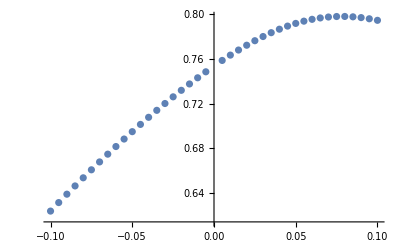

```mathematica
P = ListPlot[{{-0.005,0.7484834098231707},{-0.01,0.7431140795450425},{-0.015,0.7375757378693601},{-0.02,0.7318790089540628},{-0.025,0.7260330935826821},{-0.03,0.7200458852984055},{-0.035,0.7139240888131906},{-0.04,0.7076733346013035},{-0.045,0.701298285933513},{-0.05,0.6948027362988493},{-0.055,0.6881896963223565},{-0.06,0.6814614700458248},{-0.065,0.6746197209042067},{-0.07,0.6676655280468112},{-0.075,0.6605994333068429},{-0.08,0.6534214807725982},{-0.085,0.6461312476330291},{-0.09,0.6387278689614306},{-0.095,0.6312100557660517},{-0.1,0.6235761071573053},{0.005,0.758664819246358},{0.01,0.7634477314478979},{0.015,0.7680032863802935},{0.02,0.7723129532088566},{0.025,0.7763569302391824},{0.03,0.7801145197103546},{0.035,0.7835646592496984},{0.04,0.7866866080425511},{0.045,0.7894607612579949},{0.05,0.7918695375424517},{0.055,0.7938982578891333},{0.06,0.79553591832393},{0.065,0.7967757610431646},{0.07,0.7976155717130281},{0.075,0.7980576705282044},{0.08,0.7981086111893011},{0.085,0.797778642880953},{0.09,0.797081016013443},{0.095,0.796031219300202},{0.1,0.794646226161407}}]
```

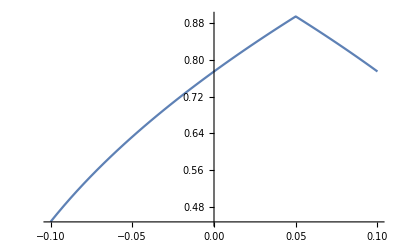

```mathematica
G = Plot[Sqrt[1+2(0.2*Cos[Inv[0.2,J]]+2*J*Cos[2*Inv[0.2,J]])],{J,-0.1,0.1}]
```

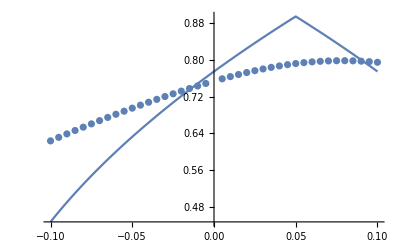

```mathematica
Show[G,P]
```

```mathematica
Manipulate[Plot[j1*Cos[k]+j2*Cos[2*k],{k,-Pi,Pi}],{j1,-1,1},{j2,-1,1}]
```

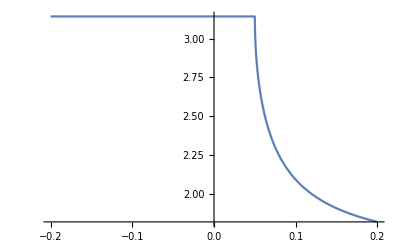

```mathematica
Plot[Inv[0.2,J],{J,-0.2,0.2}]
```

```mathematica
'
```

```mathematica
√(J^4/(J^2+J p)+(J^3 p)/(J^2+J p)+(J^2 p^2)/(2 (J^2+J p))+(J p^3)/(8 (J^2+J p))-1/(8 (J^2+J p))(√(256 J^4 J q^2+512 J^3 J q^2 p+64 J^6 p^2+320 J^2 J q^2 p^2+96 J^5 p^3+64 J  J q^2 p^3+52 J^4 p^4+12 J^3 p^5+J^2 p^6)))/.{J->1, p->2*-0.1,q->0.2}
```

0.753672